## 1. Package

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["methodSugiyama`"]
ClearAll["methodSugiyama`*"]
Get["methodSugiyama`"]
```

C:\Users\shiro\Desktop\full\6 семестр\7 семестр\git-repo\texnotes-7th-semester\6. Планирование расписаний и управление доходами\HT\HT7 20.09.2020 22.00\new_package

```mathematica
?methodSugiyama`*
```

## 1.1 GetGraph

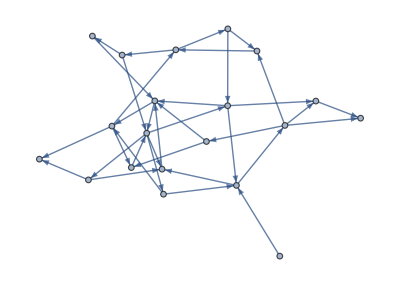

```mathematica
graph=GetGraph[20,0.1]
```

## 1.2 Example Order

```mathematica
getOrderRandom[graph]
```

{12,10,2,18,7,14,20,4,6,5,11,3,16,19,17,15,1,8,9,13}

```mathematica
BFSearch[graph]
```

{1,9,15,3,5,13,17,7,8,4,12,2,6,11,18,20,10,19,14}

```mathematica
DDVertex[graph]
```

{4,7,12,9,17,11,6,5,20,18,3,1,16,10,13,14,8,15,19,2}

```mathematica
DFSearch[graph]
```

{6,4,14,8,9,18,20,5,12,10,17,19,1,15,3,13,7,2,11,16}

## 1.3 Random order

```mathematica
result= GetDAG[graph,ApproachOption->"Random order"]
```

<|acyclic graph→{3->7,3->8,4->8,4->9,4->18,4->20,6->14,7->2,7->11,7->15,11->5,12->10,12->17,12->19,13->2,17->1,17->6,20->8,20->19},feedback set→{1->9,1->15,5->4,5->12,6->4,7->13,8->5,9->3,9->5,9->13,10->4,11->10,14->5,15->17,16->3,18->3,18->12}|>

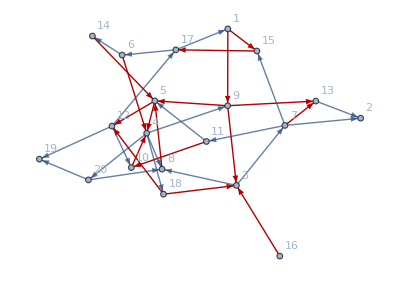

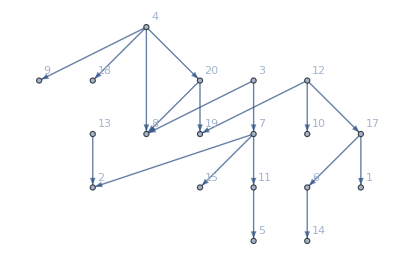

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.4 BFS Order

```mathematica
result=GetDAG[graph,ApproachOption->"BFS order"]
```

<|acyclic graph→{1->9,1->15,3->7,3->8,4->18,4->20,5->4,5->12,6->14,7->2,7->11,9->3,9->5,9->13,11->10,12->10,12->19,13->2,15->17,17->6,20->19},feedback set→{4->8,4->9,6->4,7->13,7->15,8->5,10->4,11->5,12->17,14->5,16->3,17->1,18->3,18->12,20->8}|>

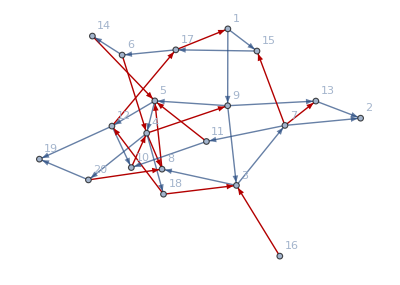

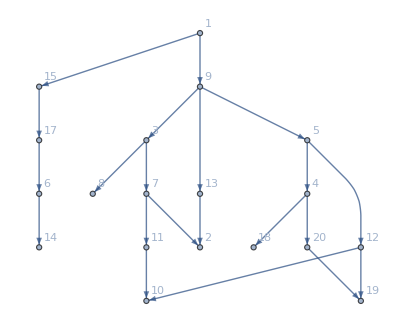

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.5 DFS Order

```mathematica
result=GetDAG[graph,ApproachOption->"DFS Order"]
```

<|acyclic graph→{1->15,3->7,4->8,4->9,4->18,4->20,5->12,6->4,6->14,7->2,7->11,8->5,9->3,9->5,9->13,12->10,12->17,12->19,13->2,14->5,17->1,18->3,18->12,20->19},feedback set→{1->9,3->8,5->4,7->13,7->15,10->4,11->5,11->10,15->17,16->3,17->6,20->8}|>

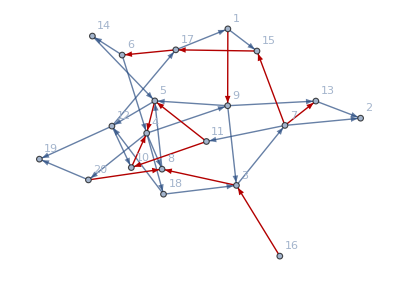

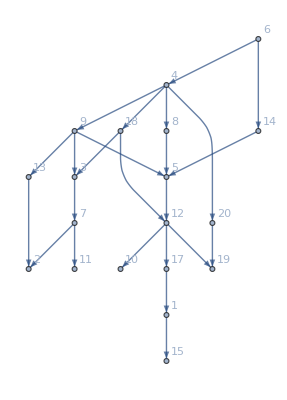

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.6 VertexOutDegree Order

```mathematica
result=GetDAG[graph,ApproachOption->"VertexOutDegree Order"]
```

<|acyclic graph→{1->15,3->8,4->8,4->9,4->18,4->20,6->14,7->2,7->11,7->13,7->15,9->3,9->5,9->13,11->5,11->10,12->10,12->17,12->19,13->2,17->1,17->6,18->3,20->8,20->19},feedback set→{1->9,3->7,5->4,5->12,6->4,8->5,10->4,14->5,15->17,16->3,18->12}|>

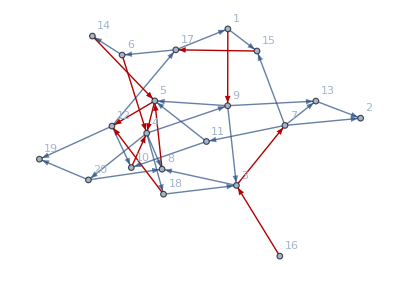

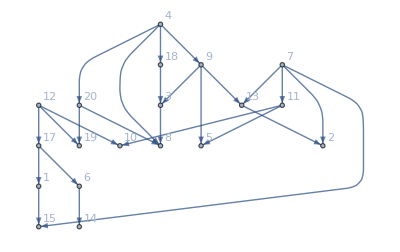

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.7 Greedy Cycle Removal

```mathematica
result=GetDAG[graph,ApproachOption->"Cycle Removal"]
```

<|acyclic graph→{3->8,4->8,4->9,4->18,4->20,6->4,6->14,7->11,7->13,9->3,9->13,12->17,12->19,16->3,17->1,18->3,18->12,20->8,20->19},feedback set→{1->9,1->15,3->7,5->4,5->12,7->2,7->15,8->5,9->5,10->4,11->5,11->10,12->10,13->2,14->5,15->17,17->6}|>

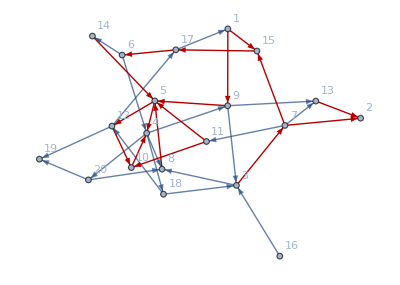

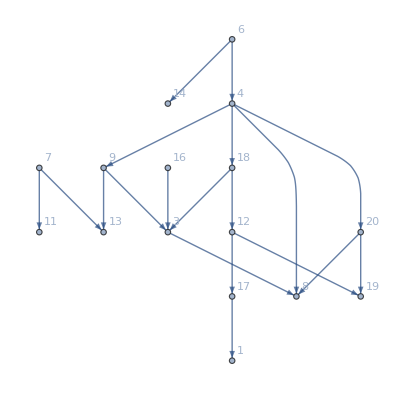

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.8 Set Covering Formulation

```mathematica
result=GetDAG[graph,ApproachOption->"IP SCF"]
```

<|acyclic graph→{1->9,1->15,3->7,3->8,4->8,4->9,4->18,4->20,5->12,6->4,6->14,7->2,7->11,7->13,7->15,8->5,9->3,9->5,9->13,11->5,11->10,12->10,12->19,13->2,14->5,16->3,17->1,17->6,18->3,18->12,20->8,20->19},feedback set→{5->4,10->4,12->17,15->17}|>

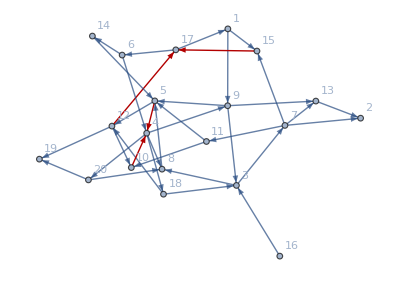

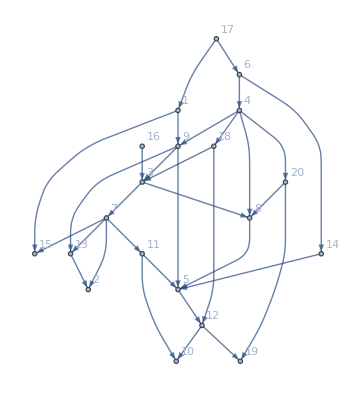

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.9 Triangle Rule

```mathematica
result=GetDAG[graph,ApproachOption->"IP TI"]
```

<|acyclic graph→{1->9,1->15,3->7,3->8,4->9,5->4,6->4,6->14,7->15,10->4,11->5,12->10,12->17,12->19,16->3,17->1,17->6,20->8},feedback set→{4->8,4->18,4->20,5->12,7->2,7->11,7->13,8->5,9->3,9->5,9->13,11->10,13->2,14->5,15->17,18->3,18->12,20->19}|>

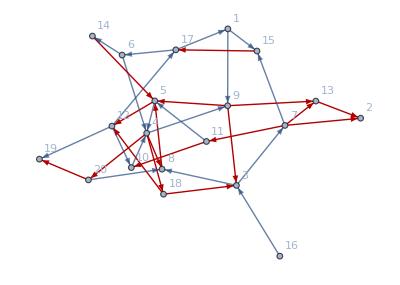

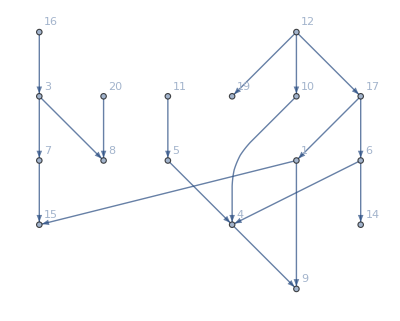

```mathematica
Graph[graph,GraphHighlight->result["feedback set"],VertexLabels->"Name"]
Graph[result["acyclic graph"],VertexLabels->"Name"]
```

## 1.10 Test Mistakes

```mathematica
GetDAG[graph,ApproachOption->"IPTI"]
```

GetDAG::option: Option IPTI is not in list of options. Choose another one from the list: 
Random order
BFS order
DFS Order
VertexOutDegree Order
Cycle Removal
IP SCF
IP TI

$Aborted

```mathematica
GetDAG[graph,ApproachOption->"IP TI",ResultOption->"fulle"]
```

GetDAG::RESoption: Option fulle is not in list of ResOptions. Choose another one from the list: 
full
acyclic graph
feedback set

$Aborted

```mathematica
GetDAG[graph,ApproachOption->"IP TI",ResultOption->"full"]
```

<|acyclic graph→{1->9,1->15,3->7,3->8,4->9,5->4,6->4,6->14,7->15,10->4,11->5,12->10,12->17,12->19,16->3,17->1,17->6,20->8},feedback set→{4->8,4->18,4->20,5->12,7->2,7->11,7->13,8->5,9->3,9->5,9->13,11->10,13->2,14->5,15->17,18->3,18->12,20->19}|>

```mathematica
GetDAG[graph,ApproachOption->"IP TI",ResultOption->"acyclic graph"]
```

{1->9,1->15,3->7,3->8,4->9,5->4,6->4,6->14,7->15,10->4,11->5,12->10,12->17,12->19,16->3,17->1,17->6,20->8}

```mathematica
GetDAG[graph,ApproachOption->"IP TI",ResultOption->"feedback set"]
```

{4->8,4->18,4->20,5->12,7->2,7->11,7->13,8->5,9->3,9->5,9->13,11->10,13->2,14->5,15->17,18->3,18->12,20->19}

## 2. Layering

## 2.1 The Longest-Path Algorithm

```mathematica
LayeringLongestPath[getDagResult_]:=Module[{g=Graph[getDagResult["acyclic graph"],VertexLabels->"Name"],U={},Z={},L={},currentLayer=1,V,relations,v,dop,mask},
V=Sort@VertexList[g];
relations=Association[Table[v-><|"ребенок для вершин"->Cases[IncidenceList[g,v],e_->h_/;h==v->e],
"родитель для вершин"->Cases[IncidenceList[g,v],e_->h_/;e==v->h]|>,{v,V}]];
While[
!Union[U]===V(*пока не обойдем все вершины*),
dop=Complement[V,U];(*разность множеств V \ U*)
mask=Table[SubsetQ[Z,relations[i]["ребенок для вершин"]],{i,dop}];
v=Pick[dop,mask,True];(*рассматриваем вершины, у которых все все дети лежат в множестве Z*)
Which[v!={},(*v has been selected - если вершины существуют, то возьмем первую*)
AppendTo[L,{currentLayer,First[v]}];(*добавляем вершнину на слой currentLayer*)
AppendTo[U,First[v]],
v=={},(*no vertext has been selected*)
currentLayer=currentLayer+1;
Z=Z∪U];
];
<|"acyclic graph"->getDagResult["acyclic graph"], "feedback set"->getDagResult["feedback set"],"layers"->GatherBy[L,First][[All,All,2]]|>

]
```

```mathematica
g=GetGraph[10,0.1];
```

```mathematica
layersResult=LayeringLongestPath[GetDAG[g, ApproachOption -> "IP SCF", ResultOption -> "full"]]
```

<|acyclic graph→{2->1,2->4,4->1,4->6,6->9,8->2,8->7,9->3,10->2,10->3,10->5},feedback set→{3->9,3->10,9->6},layers→{{8,10},{2,5,7},{4},{1,6},{9},{3}}|>

## 2.2

```mathematica
LayeringExact[getDagResult_]:=Module[{g=Graph[getDagResult["acyclic graph"],VertexLabels->"Name"],A=getDagResult["acyclic graph"],V,λvars,cond1,objfun,c,m,b,lu,domain,solution,l,λ},
V=Sort@VertexList@g;
λvars=λ/@V;
cond1=Cases[A,in_->two_-> λ[two]-λ[in]];
objfun=Total@cond1;
c=Last@CoefficientArrays[objfun,λvars];
m=Last@CoefficientArrays[cond1,λvars];
b=ConstantArray[{1,1},Length[A]];
lu=ConstantArray[{0,Infinity},Length[λvars]];
domain=ConstantArray[Integers,Length[λvars]];
solution=Quiet[LinearProgramming[c,m,b,lu,domain]];
l=SortBy[GatherBy[Thread[{V,solution}],Last],#⟦1,2⟧&]⟦All,All,1⟧;
<|"acyclic graph"->getDagResult["acyclic graph"], "feedback set"->getDagResult["feedback set"],"layers"->l|>
]
```

```mathematica
g=GetGraph[10,0.1];
layersResult=LayeringExact[GetDAG[g,ApproachOption->"IP SCF",ResultOption->"full"]]
```

<|acyclic graph→{1->2,3->10,4->1,4->10,5->2,5->9,8->6,8->7,9->1,9->7,10->6,10->9},feedback set→{1->4},layers→{{3,4},{5,8,10},{6,9},{1,7},{2}}|>

## 3. Test GetLayering

```mathematica
g=GetGraph[10,0.1];
```

```mathematica
GetLayering[GetDAG[g,ApproachOption->"IP SCF",ResultOption->"full"],ApproachOption->"Longest Path"]
```

<|acyclic graph→{2->3,3->9,4->3,5->1,5->2,6->10,7->9,7->10,8->3,8->4,9->1,9->10},feedback set→{10->4},layers→{{5,6,7,8},{2,4},{3},{9},{1,10}}|>

```mathematica
GetLayering[GetDAG[g,ApproachOption->"IP SCF",ResultOption->"full"],ApproachOption->"Exact"]
```

<|acyclic graph→{2->3,3->9,4->3,5->1,5->2,6->10,7->9,7->10,8->3,8->4,9->1,9->10},feedback set→{10->4},layers→{{5,8},{2,4},{3,7},{6,9},{1,10}}|>

```mathematica
GetLayering[GetDAG[g,ApproachOption->"IP SCF",ResultOption->"full"],ApproachOption->"Exacte"]
```

GetLayering::option: Option Exacte is not in list of options. Choose another one from the list: 
Longest Path
Exact

$Aborted

```mathematica
GetLayering[GetDAG[g,ApproachOption->"IP SCF",ResultOption->"full"]]
```

<|acyclic graph→{2->3,3->9,4->3,5->1,5->2,6->10,7->9,7->10,8->3,8->4,9->1,9->10},feedback set→{10->4},layers→{{5,6,7,8},{2,4},{3},{9},{1,10}}|>